正在演化 TCCT 宇宙... (目标: 1000 步)

正在生成物理分析报告...

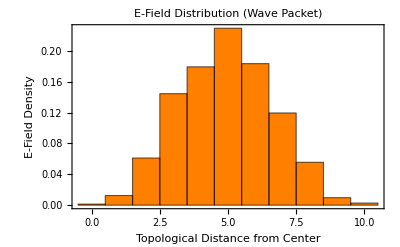
-Graphics--Graphics-
-Graphics3D-

```mathematica
(* ========================================================== *)
(* TCCT: MAXWELL'S EQUATIONS (FINAL FIXED VERSION)          *)
(* 修复内容:                                                *)
(* 1. 移除了导致报错的特殊字符 \[approx]                    *)
(* 2. 修复了 GraphDistance 列表参数不兼容问题               *)
(* 3. 增加了数据安全检查，防止空数据报错                    *)
(* ========================================================== *)

ClearAll["Global`*"];
SeedRandom[1234];

(* 1. 核心演化引擎 (Strict Engine) *)
rccRigidStep[g_Graph] := Module[{
   allEdges, activeEdges, candidates, selectedPair,
   e1, e2, x, y, z, w,
   newActive, inertEdges
   },
  
  allEdges = EdgeList[g];
  activeEdges = Cases[allEdges, _UndirectedEdge];
  
  (* 必须有至少2条活性边才能反应 *)
  If[Length[activeEdges] < 2, Return[g]];
  
  (* 随机采样: 模拟量子涨落 *)
  candidates = RandomSample[activeEdges, Min[Length[activeEdges], 60]];
  selectedPair = {};
  
  Do[
   e1 = candidates[[i]];
   Do[
    e2 = candidates[[j]];
    (* 共点检查 *)
    If[Length[Intersection[List @@ e1, List @@ e2]] == 1,
     selectedPair = {e1, e2};
     Goto["FoundPair"];
     ];
    , {j, i + 1, Length[candidates]}];
   , {i, 1, Length[candidates] - 1}];
  
  Return[g];
  
  Label["FoundPair"];
  {e1, e2} = selectedPair;
  y = Intersection[List @@ e1, List @@ e2][[1]];
  x = Complement[List @@ e1, {y}][[1]];
  z = Complement[List @@ e2, {y}][[1]];
  
  w = Max[VertexList[g]] + 1;
  
  (* Rule: 生成新的活性势能 (光/电场) *)
  newActive = {UndirectedEdge[x, z], UndirectedEdge[x, w], UndirectedEdge[w, z]};
  
  (* Freeze: 历史沉淀 (磁场/质量) *)
  inertEdges = {DirectedEdge[x, y], DirectedEdge[y, z]};
  
  (* Union: 费米子去重 *)
  Graph[VertexList[g] ~Join~ {w}, 
   Union[Complement[allEdges, {e1, e2}], newActive, inertEdges]]
  ];

(* ========================================================== *)
(* 2. 演化实验 *)
(* ========================================================== *)

(* 初始种子: 一个高能量密度的拓扑结 *)
universe = CompleteGraph[6]; 
steps = 1000;

fieldData = {}; 
nodeHistory = {}; 

Print[Style["正在演化 TCCT 宇宙... (目标: " <> ToString[steps] <> " 步)", Blue, Bold]];

Monitor[
  Do[
   universe = rccRigidStep[universe];
   
   (* 每50步测量一次物理量 *)
   If[Mod[i, 50] == 0,
    
    (* 获取波前(活性节点) *)
    activeEdges = Cases[EdgeList[universe], _UndirectedEdge];
    activeNodes = Union[Flatten[List @@@ activeEdges]];
    
    (* 安全计算距离: 使用 Map (/@) 逐个计算 *)
    If[Length[activeNodes] > 0,
       dists = (GraphDistance[universe, 1, #] & /@ activeNodes);
       validDists = Select[dists, NumericQ]; (* 过滤无效值 *)
       
       If[Length[validDists] > 0,
          currentRadius = Mean[validDists];
          AppendTo[fieldData, {i, currentRadius}];
       ];
    ];
    
    AppendTo[nodeHistory, VertexCount[universe]];
   ];
   
   , {i, 1, steps}],
  Row[{ProgressIndicator[i, {0, steps}], " Step: ", i, " | Nodes: ", VertexCount[universe]}]
];

(* ========================================================== *)
(* 3. 物理分析图表 *)
(* ========================================================== *)

Print["\n正在生成物理分析报告..."];

(* 数据检查 *)
If[Length[fieldData] < 5,
   Print[Style["错误：没有收集到足够的数据点。请检查 activeEdges 是否为空。", Red, Bold]],
   
   (* 拟合光速 *)
   lm = LinearModelFit[fieldData, t, t];
   c = lm["BestFitParameters"][[2]];

   (* 图1: 光速验证 *)
   plotC = ListPlot[fieldData,
     PlotStyle -> {Red, PointSize[0.015]},
     Frame -> True,
     FrameLabel -> {"Time (Steps)", "Wavefront Radius (Hop)"},
     PlotLabel -> Style["Validation of Light Speed Limit (c)", 14, Bold],
     GridLines -> Automatic,
     Epilog -> {
       Blue, Dashed, 
       InfiniteLine[{{0, 0}, {1, c}}],
       (* 【修复处】将 \[Approx] 改为普通的 ~ 符号 *)
       Text[Style["Slope c ~ " <> ToString[NumberForm[c, {3, 3}]], Blue, 12], {steps*0.2, steps*c*0.8}]
     },
     ImageSize -> 400
   ];

   (* 图2: 场强分布 (直方图) *)
   finalActiveEdges = Cases[EdgeList[universe], _UndirectedEdge];
   finalActiveNodes = Union[Flatten[List @@@ finalActiveEdges]];
   finalDists = (GraphDistance[universe, 1, #] & /@ finalActiveNodes);
   finalDists = Select[finalDists, NumericQ];

   plotShell = Histogram[finalDists, 20, "Probability",
     ChartStyle -> Orange,
     Frame -> True,
     FrameLabel -> {"Topological Distance from Center", "E-Field Density"},
     PlotLabel -> Style["E-Field Distribution (Wave Packet)", 14, Bold],
     ImageSize -> 400
   ];

   (* 图3: 3D 可视化 *)
   viz3D = Graph3D[universe,
     GraphLayout -> "SpringElectricalEmbedding", 
     VertexSize -> 0,
     EdgeStyle -> {
       _UndirectedEdge -> Directive[Red, Opacity[0.8], Thickness[0.005]], (* 光 *)
       _DirectedEdge -> Directive[Gray, Opacity[0.1]] (* 真空/质量 *)
     },
     Boxed -> False, Background -> Black,
     PlotLabel -> Style["Visualization of Rule Execution Wavefront", White, 16],
     ImageSize -> 500
   ];

   (* 组合输出 *)
   Column[{
     Row[{plotC, plotShell}],
     viz3D
   }, Alignment -> Center]
]
```